```mathematica
ClearAll;
a=7.857 (* L^2 bar / mol^2 *);
b=0.087  (* L / mol *);
R= 0.0831 (* L*bar/K*mol *);
```

```mathematica
P[Bm_,T_]:=R T /(Bm -b) -a/Bm^2
```

```mathematica
Plot[P[Bm,300],{Bm,0,10},PlotRange->{{0,10},{0,40}}]
```

-Graphics-

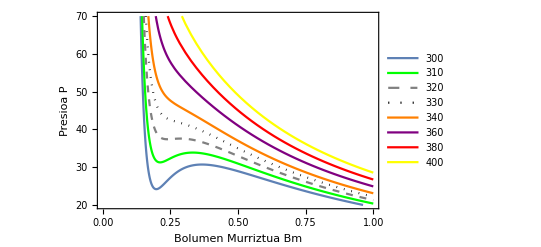

```mathematica
t300=Plot[P[Bm,300],{Bm,0,1},  PlotRange->{{0,1},{20,70}}, Frame->True,FrameLabel->{Style[Row[{"Bolumen Murriztua ", Bm}],14],Style[Row[{"Presioa ",P}],14]},PlotLegends->{"300"}];
t310= Plot[P[Bm,310],{Bm,0,1},PlotStyle->{{Thick,Green}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"310"}];
t320=Plot[P[Bm,320],{Bm,0,1},PlotStyle->{{Dashed,Gray}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"320"}];
t330= Plot[P[Bm,330],{Bm,0,1},PlotStyle->{{Dotted,Black}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"330"}];
t340= Plot[P[Bm,340],{Bm,0,1},PlotStyle->{{Orange}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"340"}];
t360=Plot[P[Bm,360],{Bm,0,1},PlotStyle->{{Purple}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"360"}];
t380= Plot[P[Bm,380],{Bm,0,1},PlotStyle->{{Red}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"380"}];
t400= Plot[P[Bm,400],{Bm,0,1},PlotStyle->{{Yellow}}, PlotRange->{{0,1},{20,70}},PlotLegends->{"400"}];

Show[t300,t310,t320,t330,t340,t360,t380,t400]
```

```mathematica
Pideal[Bm_,T_]:=R T/Bm;
```

```mathematica
Manipulate[Plot[{P[Bm,T],Pideal[Bm,T]},{Bm,0,1},PlotRange->{{0,1},{20,70}},PlotLegends->{T}],{T,300,380,5}]
```